```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/Band_life_broadened"];
phononSE=ReadList["se.all.Gamma.Gamma-X.X.X-W.W.W-K.K.K-Gamma.Gamma-L.L",{Number, Number,Number, Number,Number, Number,Number, Number,Number, Number,Number}];
```

```mathematica
path={{0,0,0},{0,0,0},0.5({0,0,0}+{0,0.5,0.5}),{0,0.5,0.5},0.5({0,0.5,0.5}+{0.25,0.75,0.5}),{0.25,0.75,0.5},0.5({0.25,0.75,0.5}+{3/8,3/4,3/8}),{3/8,3/4,3/8},0.5({3/8,3/4,3/8}+{0,0,0}),{0,0,0},0.5({0,0,0}+{1/2,1/2,1/2}),{1/2,1/2,1/2}}
pathNorm=Table[Norm[path[[i]]-path[[i-1]]],{i,2,12}]
pathD=Table[Total@Table[pathNorm[[i]],{i,1,j}],{j,1,11}]
```

{{0,0,0},{0,0,0},{0.,0.25,0.25},{0,0.5,0.5},{0.125,0.625,0.5},{0.25,0.75,0.5},{0.3125,0.75,0.4375},{3/8,3/4,3/8},{0.1875,0.375,0.1875},{0,0,0},{0.25,0.25,0.25},{1/2,1/2,1/2}}

{0,0.353553,0.353553,0.176777,0.176777,0.0883883,0.0883883,0.459279,0.459279,0.433013,0.433013}

{0,0.353553,0.707107,0.883883,1.06066,1.14905,1.23744,1.69672,2.156,2.58901,3.02202}

```mathematica
pList=Table[Table[pathD[[j]],{i,1,201}],{j,1,11}];
```

```mathematica
ListPointPlot3D[Table[Transpose[{Transpose[phononSE][[1]],pList[[j]],Transpose[phononSE][[j+1]]}],{j,1,10}]]
```

-Graphics3D-

```mathematica
"Gamma Gamma-X X X-W W W-K K K-Gamma Gamma-L L"
```

Gamma Gamma-X X X-W W W-K K K-Gamma Gamma-L L

```mathematica
popts3D={BoxRatios->{1.5,1,0.6},Filling->Bottom,PlotTheme->"Scientific",AxesLabel->{Style["ω (THz)",18,Black],Style["q (1/Å)",18,Black],Style["Γ''(ω)  ",18,Black]" \n(THz)  "},AxesStyle->Directive[18,Black,Thickness[0.004]],Boxed->False,BoxStyle->Directive[Thickness[0.00001],Dashing[0.02]],PlotStyle->Directive[Black,PointSize[0.006]],Ticks->{{10,20,30},{{0,"Γ"},{0.35,"Γ-X"},{0.7,"X"},{0.83,""},{1.00,"W"},{1.15,""},{1.3,"K"},{1.7,"K-Γ"},{2.1,"Γ-L"},{2.6,"L"}},Automatic
},FillingStyle->Directive[Thickness[1],Orange,Thin,Opacity[1]],ImageSize->850,PlotRange->{{5,38},Full,{0,0.24}}};
```

```mathematica
gammaData=Table[Transpose[{Transpose[phononSE][[1]],pList[[j]],Transpose[phononSE][[j+1]]}],{j,1,10}];
```

```mathematica
ListPointPlot3D[gammaData,ImageSize->500,Evaluate@popts3D]/.Point[a___]:>{Thickness[0.004],Line[a]}
```

-Graphics3D-

```mathematica
"https://en.wikipedia.org/wiki/Kramers%E2%80%93Kronig_relations"
```

```mathematica
Transpose[gammaData[[1]]][[1]][[-1]]
```

40.4167

```mathematica
im[x_]:=If[0≤ x≤Transpose[gammaData[[1]]][[1]][[-1]],Interpolation[Transpose[{Transpose[gammaData[[1]]][[1]],Transpose[gammaData[[1]]][[3]]}]][x],0]
```

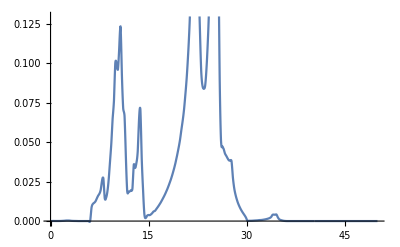

```mathematica
Plot[im[x],{x,0,50}]
```

```mathematica
re[y_]:=Integrate[(-2y/Pi)*im[x]/(x^2-y^2),{x,0,Infinity},PrincipalValue->True,GenerateConditions->False,Assumptions->x>0&&Element[x,Reals]]//N
```

```mathematica
sin=Table[{i*2Pi/10,Sin[i*2Pi/10]//N},{i,0,10}]
```

{{0,0.},{π/5,0.587785},{(2 π)/5,0.951057},{(3 π)/5,0.951057},{(4 π)/5,0.587785},{π,0.},{(6 π)/5,-0.587785},{(7 π)/5,-0.951057},{(8 π)/5,-0.951057},{(9 π)/5,-0.587785},{2 π,0.}}

```mathematica
resin[y_]:=Integrate[(-2y/Pi)*Sin[x*2Pi/10]/(x^2-y^2),{x,0,Infinity},PrincipalValue->True,GenerateConditions->False]//N
resinList=Table[{i*2Pi/10,resin[i]//N},{i,0,10}]
```

{{(i π)/5,Sin[0.628319 i]},{(i π)/5,Sin[0.628319 i]},{(i π)/5,Sin[0.628319 i]},{(i π)/5,Sin[0.628319 i]},{(i π)/5,Sin[0.628319 i]},{(i π)/5,Sin[0.628319 i]},{(i π)/5,Sin[0.628319 i]},{(i π)/5,Sin[0.628319 i]},{(i π)/5,Sin[0.628319 i]},{(i π)/5,Sin[0.628319 i]}}

{{0,0.},{π/5,-0.310822},{(2 π)/5,0.0374273},{(3 π)/5,0.574071},{(4 π)/5,1.023},{π,1.17898},{(6 π)/5,0.96257},{(7 π)/5,0.443302},{(8 π)/5,-0.189812},{(9 π)/5,-0.701918},{2 π,-0.902823}}

```mathematica
sinInter1[z_]:=If[z≥ 0&&z≤ 2*Pi,Interpolation[sin][z],0]
```

```mathematica
sin=Table[{i*2Pi/10,Sin[i*2Pi/10]//N},{i,0,10}]
```

{{0,0.},{π/5,0.587785},{(2 π)/5,0.951057},{(3 π)/5,0.951057},{(4 π)/5,0.587785},{π,0.},{(6 π)/5,-0.587785},{(7 π)/5,-0.951057},{(8 π)/5,-0.951057},{(9 π)/5,-0.587785},{2 π,0.}}

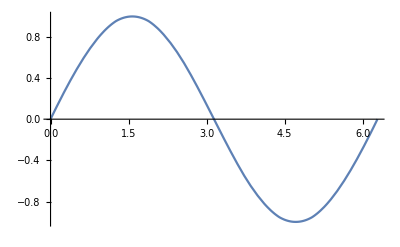

```mathematica
Plot[Evaluate[sinInter1[z]],{z,0,2Pi}]
```

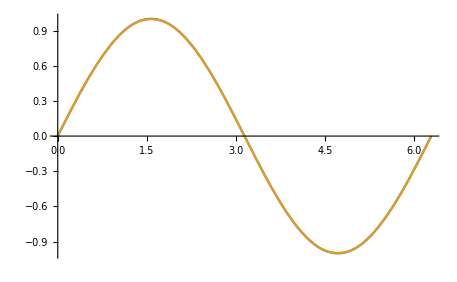

```mathematica
Plot[{Sin[z],sinInter1[z]},{z,0,2Pi}]
```

```mathematica
resinInter[y_]:=Integrate[(-2y/Pi)*Evaluate@(sinInter1[z]/.z->x)/(x^2-y^2),{x,0,Infinity},PrincipalValue->True,GenerateConditions->False,Assumptions->x>0&&y>0&&x∈Reals]//N
resinListInter=Table[{i*2Pi/10,resinInter[i]//N},{i,1,10}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.00015}. NIntegrate obtained -6.74469 and 6.66479 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.0003}. NIntegrate obtained -0.682581 and 1.64029 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {3.00046}. NIntegrate obtained 0.939522 and 0.320357 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{π/5,-6.74469},{(2 π)/5,-0.682581},{(3 π)/5,0.939522},{(4 π)/5,5.86528},{π,-1.35982},{(6 π)/5,-1.73577},{(7 π)/5,-0.170582},{(8 π)/5,-0.0861476},{(9 π)/5,-0.0521182},{2 π,-0.0346095}}

```mathematica
resinNum[y_]:=(-2y/Pi)*NIntegrate[Sin[x*2Pi/10]/(x^2-y^2),{x,0.000,2Pi},Method->"PrincipalValue",MaxRecursion->20,Exclusions->{x^2-y^2==0}]
resinListNum=Table[{i*2Pi/10,resinNum[i]//N},{i,1,10}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in x near {x} = {1.00001}. NIntegrate obtained -1.9917 and 2.90242 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in x near {x} = {2.00001}. NIntegrate obtained 1.23851 and 1.52813 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 20 recursive bisections in x near {x} = {3.}. NIntegrate obtained -0.455033 and 0.542499 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{{π/5,1.26795},{(2 π)/5,-1.57692},{(3 π)/5,0.86905},{(4 π)/5,-0.378659},{π,0.960728},{(6 π)/5,-0.760799},{(7 π)/5,0.191841},{(8 π)/5,0.204638},{(9 π)/5,0.189059},{2 π,0.172184}}

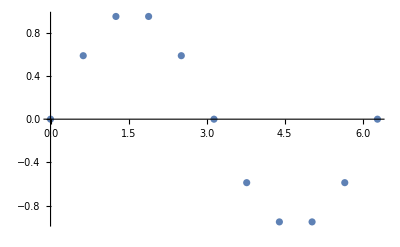

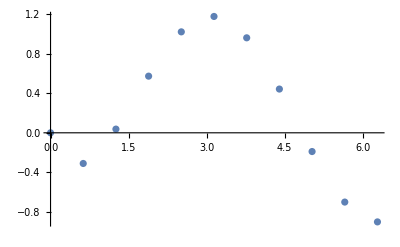

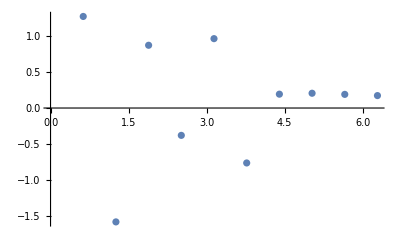

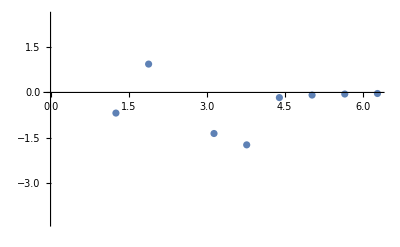

```mathematica
ListPlot[sin]
ListPlot[resinList]
ListPlot[resinListNum]
ListPlot[resinListInter]
```

```mathematica
imList=Table[{i,im[i]},{i,1,40}]
```

{{1,0.0000427728},{2,0.00018426},{3,0.000269376},{4,0.0000492741},{5,7.51164×10^-6},{6,-0.000490409},{7,0.013585},{8,0.0275843},{9,0.0321114},{10,0.101561},{11,0.0818102},{12,0.0186618},{13,0.0341719},{14,0.0336844},{15,0.00382202},{16,0.00660461},{17,0.0128862},{18,0.0217499},{19,0.0350019},{20,0.0574786},{21,0.10247},{22,0.289068},{23,0.0997826},{24,0.10862},{25,0.338571},{26,0.0606004},{27,0.0403681},{28,0.0235236},{29,0.00826478},{30,0.00110477},{31,0.000278776},{32,0.000632703},{33,0.00124274},{34,0.00405083},{35,0.00108379},{36,0.0000299597},{37,2.69997×10^-9},{38,4.05076×10^-9},{39,1.72385×10^-9},{40,3.61658×10^-11}}

```mathematica
reList=Table[{i,re[i]},{i,1,40}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{1,-0.00362743},{2,-0.00771477},{3,-0.0109673},{4,-0.0158439},{5,-0.0222219},{6,-0.0472194},{7,-0.0122976},{8,-0.0730148},{9,-0.098953},{10,0.0075181},{11,0.112103},{12,0.0183538},{13,0.062816},{14,-0.482434},{15,-0.0071658},{16,-0.0215971},{17,-0.0441511},{18,-0.0545318},{19,-0.0821781},{20,-0.125274},{21,-0.255348},{22,-1.62887},{23,0.333966},{24,-0.0176311},{25,0.0712271},{26,0.404246},{27,0.179681},{28,0.185327},{29,0.086928},{30,0.0774515},{31,0.0654991},{32,0.0575704},{33,0.0508219},{34,0.0047255},{35,0.050948},{36,0.0430668},{37,0.0399928},{38,0.0375675},{39,0.0355116},{40,0.0337229}}

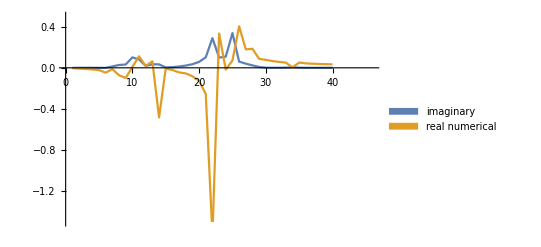

```mathematica
ListPlot[{imList,reList},Joined->True,PlotRange->{{0,46},{-1.5,0.5}},PlotLegends->SwatchLegend[{"imaginary","real numerical","real analytic"}]]
```

```mathematica
real2[y_]:=(-2/Pi)*Integrate[y*imaginary1[x]/(x^2-y^2),{x,0,Infinity},PrincipalValue->True,GenerateConditions->False,Assumptions->x>0&&y>0]//Quiet
```

```mathematica
real2[10]//N
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {10.0004}. NIntegrate obtained -0.0119102 and 0.222404 for the integral and error estimates.

0.0075823

```mathematica
Plot[real2[y],{y,0,10}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.000249075}. NIntegrate obtained 1.3658×10^-6 and 8.25546×10^-8 for the integral and error estimates.

Plot::exclul: {(x^2-y^2)-0} must be a list of equalities or real-valued functions.

$Aborted

```mathematica
real[y_]:=(-2/Pi)*NIntegrate[y*imaginary1[x]/(x^2-y^2),{x,0,30},Method->"PrincipalValue",MaxRecursion->20,Exclusions->{(x^2-y^2)==0}]//Quiet
```

```mathematica
realNumerical[y_]:=(-2/Pi)*NIntegrate[y*imaginary1[x]/(x^2-y^2),{x,1,Infinity},Method->"PrincipalValue",MaxRecursion->20]//Quiet
```

```mathematica
realList2//Length
```

NIntegrate::inumr: The integrand (4.3«1»InterpolatingFunction[{{0.,40.4167}},{5,7,0,{201},{4},0,0,0,0,Automatic,{},{},False},«1»,{Developer`PackedArrayForm,{0,«49»,«152»},{0.,0.0000326209,0.0000684285,0.0000500967,«44»,0.0762732,0.100133,«151»}},{Automatic}]«1»«1»])/(-18.49+x^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{40.4167,3.67005×10^28}}.

NIntegrate::inumr: The integrand (4.6«1»InterpolatingFunction[{{0.,40.4167}},{5,7,0,{201},{4},0,0,0,0,Automatic,{},{},False},«1»,{Developer`PackedArrayForm,{0,«49»,«152»},{0.,0.0000326209,0.0000684285,0.0000500967,«44»,0.0762732,0.100133,«151»}},{Automatic}]«1»«1»])/(-21.16+x^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{40.4167,3.67005×10^28}}.

NIntegrate::inumr: The integrand (4.9«1»InterpolatingFunction[{{0.,40.4167}},{5,7,0,{201},{4},0,0,0,0,Automatic,{},{},False},«1»,{Developer`PackedArrayForm,{0,«49»,«152»},{0.,0.0000326209,0.0000684285,0.0000500967,«44»,0.0762732,0.100133,«151»}},{Automatic}]«1»«1»])/(-24.01+x^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{40.4167,3.67005×10^28}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

97

NIntegrate::inumr: The integrand (4.3«1»InterpolatingFunction[{{0.,40.4167}},{5,7,0,{201},{4},0,0,0,0,Automatic,{},{},False},«1»,{Developer`PackedArrayForm,{0,«49»,«152»},{0.,0.0000326209,0.0000684285,0.0000500967,«44»,0.0762732,0.100133,«151»}},{Automatic}]«1»«1»])/(-18.49+x^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{40.4167,3.67005×10^28}}.

NIntegrate::inumr: The integrand (4.6«1»InterpolatingFunction[{{0.,40.4167}},{5,7,0,{201},{4},0,0,0,0,Automatic,{},{},False},«1»,{Developer`PackedArrayForm,{0,«49»,«152»},{0.,0.0000326209,0.0000684285,0.0000500967,«44»,0.0762732,0.100133,«151»}},{Automatic}]«1»«1»])/(-21.16+x^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{40.4167,3.67005×10^28}}.

NIntegrate::inumr: The integrand (4.9«1»InterpolatingFunction[{{0.,40.4167}},{5,7,0,{201},{4},0,0,0,0,Automatic,{},{},False},«1»,{Developer`PackedArrayForm,{0,«49»,«152»},{0.,0.0000326209,0.0000684285,0.0000500967,«44»,0.0762732,0.100133,«151»}},{Automatic}]«1»«1»])/(-24.01+x^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{40.4167,3.67005×10^28}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

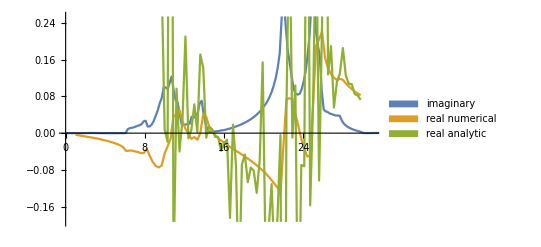

{{1.,-0.00362104},{1.3,-0.00462876},{1.6,-0.0041592},{1.9,-0.00709783},{2.2,-0.00828457},{2.5,-0.00895245},{2.8,-0.0105511},{3.1,-0.0114618},{3.4,-0.0127017},{3.7,-0.014481},{4.,-0.0158183},{4.3,-0.63662 NIntegrate[(4.3 InterpolatingFunction[{{0., 40.4167}}, <>][x])/(-18.49+x^2),{x,0.,∞}]},{4.6,-0.63662 NIntegrate[(4.6 InterpolatingFunction[{{0., 40.4167}}, <>][x])/(-21.16+x^2),{x,0.,∞}]},{4.9,-0.63662 NIntegrate[(4.9 InterpolatingFunction[{{0., 40.4167}}, <>][x])/(-24.01+x^2),{x,0.,∞}]},{5.2,-0.63662 NIntegrate[(5.2 InterpolatingFunction[{{0., 40.4167}}, <>][x])/(-27.04+x^2),{x,0.,∞}]},{5.5,-0.63662 NIntegrate[(5.5 InterpolatingFunction[{{0., 40.4167}}, <>][x])/(-30.25+x^2),{x,0.,∞}]},{5.8,-0.63662 NIntegrate[(5.8 InterpolatingFunction[{{0., 40.4167}}, <>][x])/(-33.64+x^2),{x,0.,∞}]},{6.1,-0.0395391},{6.4,-0.0399051},{6.7,-0.0353894},{7.,-0.0122528},{7.3,-0.0606642},{7.6,-0.0361523},{7.9,-0.266696},{8.2,-0.037125},{8.5,0.151397},{8.8,-0.0882438},{9.1,0.127231},{9.4,-0.0376099},{9.7,0.332112},{10.,0.0075823},{10.3,-0.0189961},{10.6,1.65626},{10.9,-0.298977},{11.2,0.0968995},{11.5,-0.040173},{11.8,0.0288763},{12.1,0.210518},{12.4,-0.0112048},{12.7,0.00723101},{13.,0.0628997},{13.3,0.0023251},{13.6,0.171474},{13.9,0.141653},{14.2,-0.00984314},{14.5,0.0138282},{14.8,0.00859203},{15.1,-0.00809304},{15.4,-0.00816636},{15.7,-0.0384261},{16.,-0.0214938},{16.3,-0.0141507},{16.6,-0.184885},{16.9,0.0184188},{17.2,-0.0685314},{17.5,-0.360151},{17.8,-0.0686552},{18.1,-0.0464902},{18.4,-0.106887},{18.7,-0.0747942},{19.,-0.0820549},{19.3,-0.130158},{19.6,-0.0594108},{19.9,0.154445},{20.2,-0.275202},{20.5,-0.211517},{20.8,-0.111052},{21.1,-0.278749},{21.4,-0.1816},{21.7,-0.00427038},{22.,-1.62872},{22.3,0.0485009},{22.6,0.481915},{22.9,-0.00972854},{23.2,0.103881},{23.5,-0.494646},{23.8,-0.069391},{24.1,-0.0723783},{24.4,0.847569},{24.7,-0.157468},{25.,0.0713909},{25.3,0.487491},{25.6,-0.103278},{25.9,0.239717},{26.2,1.4768},{26.5,0.127857},{26.8,0.189741},{27.1,0.0557791},{27.4,0.111683},{27.7,0.130166},{28.,0.185512},{28.3,0.125255},{28.6,0.107454},{28.9,0.10668},{29.2,0.085026},{29.5,0.0821822},{29.8,0.0726408}}

```mathematica
ListPlot[{imaginary1,realList,realList2[[30;;97]]},Joined->True,PlotRange->{{0,31},Automatic},PlotLegends->SwatchLegend[{"imaginary","real numerical","real analytic"}]]
```